```mathematica
CloudDeploy[FormFunction[{"profile"->"Image"},Block[{filter,img,size},

img = #profile;
filter=-Graphics-;
(* Crop the profile to the middle square *)
size=Min[ImageDimensions[img]];
img=ImageCrop[img,{size,size}];

(* Using the min ensures highest resolution *)
size=Min[size,ImageDimensions[filter]];

(* Scale images to the same size *)
img=ColorConvert[ImageResize[img,size],"Grayscale"];
filter=ImageResize[filter,size];

ImageAdjust[Blend[{img,filter}],{.1,.1}]]&,"PNG"],Permissions->"Public"]
```

```mathematica
CloudDeploy[APIFunction[{"profile"->"Image"},Block[{filter,img,size},

img = #profile;
filter=-Graphics-;
(* Crop the profile to the middle square *)
size=Min[ImageDimensions[img]];
img=ImageCrop[img,{size,size}];

(* Using the min ensures highest resolution *)
size=Min[size,ImageDimensions[filter]];

(* Scale images to the same size *)
img=ColorConvert[ImageResize[img,size],"Grayscale"];
filter=ImageResize[filter,size];

ImageAdjust[Blend[{img,filter}],{.1,.1}]]&,"PNG"],Permissions->"Public"]
```

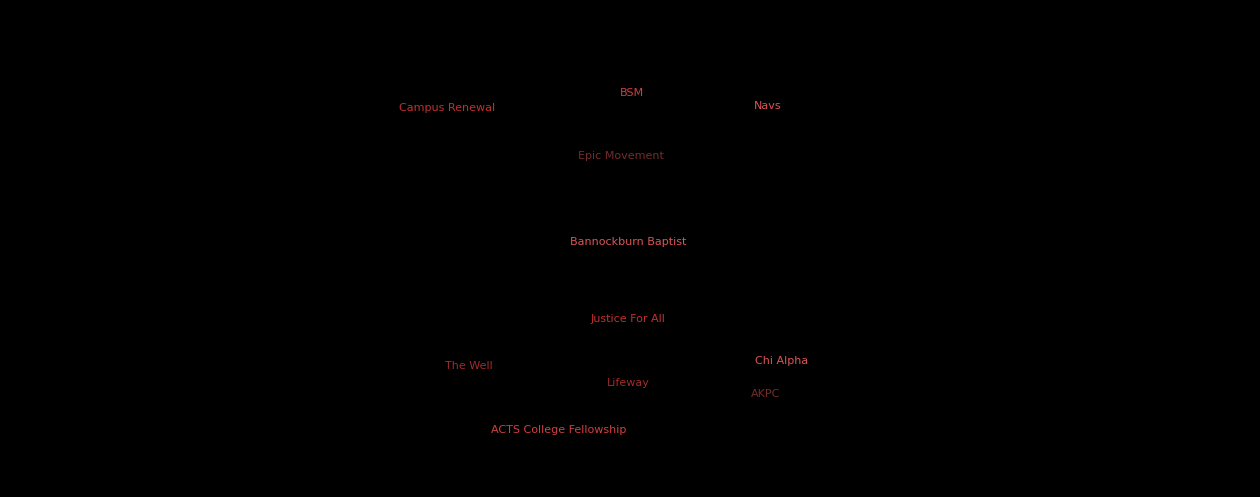

/Users/Evan/GitProjects/campusmap/RezWeekCal/wordcloud.png

```mathematica
wc=WordCloud[
{ 2->"ACTS College Fellowship",2->"Campus Renewal",7->"Epic Movement",8->"Justice For All",16->"Bannockburn Baptist",11->"BSM",2->"The Well",4->"Navs",8->"Lifeway",1->"AKPC",1->"Chi Alpha"},
Background->Transparent,ColorFunction->Reverse[Table[ColorData["CherryTones"][i],{i,0.1,.5,0.1}]],
WordSpacings->5,
ImageSize->1260]
Export["/Users/Evan/GitProjects/campusmap/RezWeekCal/wordcloud.png",wc,"PNG"]
```